# Math 350 - Lecture 11

Recursive functions

## Recursive functions

A recursive function in mathematics is a function that is defined in terms of its own preceding values. For example, the Fibonacci sequence is constructed by adding the two previous terms to generate the next term. A recursive function in Mathematica is similar - it calls itself.

Let’s define a function that will compute the Fibonacci sequence.

```mathematica
fib[0]=1;
fib[1]=1;
fib[n_]:= fib[n-1] + fib[n-2]
```

Now let us test it.

```mathematica
fib[2]
```

2

```mathematica
fib[3]
```

3

```mathematica
fib[10]
```

89

```mathematica
fib[20]
```

10946

```mathematica
fib[35]
```

14930352

Notice that computing the 50th Fibonacci number takes an absurd amount of time. Why? Let’s think about what Mathematica is actually doing when we invoke f[6], for example. Mathematica’s process is to evaluate fib[6] to get fib[5] + fib[4]. Both fib[5] and fib[4] are then evaluated to get fib[4]+fib[3] and f[3]+f[2]. Notice that Mathematica re-evaluates f[4] in each case. This continues all the way down until Mathematica finally reaches numbers that it knows, fib[0] and fib[1] and starts working its way back up.

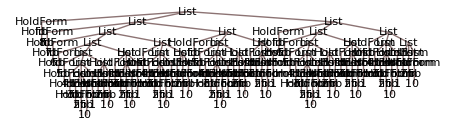

```mathematica
TreeForm[Trace[fib[8],fib[_]]]
```

We can avoid this constant re-evaluation with a technique called memoization that saves the results of the intermediate steps. Essentially, we’ll turn f into a variable assignment. This doesn’t change the output, but it stores the results of each f[n] computed along the way.

```mathematica
fib[n_]:=fib[n]=fib[n-1]+fib[n-2] (* f assigns the name f[n] to the computation of f[n] *)
```

```mathematica
fib[35]
```

14930352

Much better.

```mathematica
?fib
```

## Recursion examples

#### Problem 11.1

Write a function to compute

e(n) = 1 + 1/(1!)+1/(2!)+ ... + 1/(n!).

Let’s use recursion. We need a starting point.

```mathematica
e[0]=1;
```

Now, we’ll define the function recursively. Notice that e(1) = e(0) + 1/(1!) and e(2) = e(1) + 1/(2!) and so on. Thus, we write

```mathematica
e[n_]:= e[n]=e[n -1] + 1/n! (* note the memoization! *)
```

```mathematica
e[3]
```

8/3

```mathematica
e[6]
```

1957/720

```mathematica
e[3000]//N
```

2.71828

```mathematica
{$RecursionLimit = 6000}
```

{6000}

Note that while recursive approaches to problems are typically mathematically elegant, they can by computationally expensive. Sometimes, it is worthwhile to look at alternative approaches.

```mathematica
e2[n_]:= 1 + Plus@@(1/Range[n]!)
```

```mathematica
AbsoluteTiming[e2[1000]][[1]]
```

0.004596

```mathematica
Clear[e]
```

```mathematica
AbsoluteTiming[e[1000]][[1]]
```

0.0461158

```mathematica
AbsoluteTiming[e[1000]][[1]]
```

2.6×10^-6

Notice that on the second execution we’ve drastically increased speed (since we’ve already saved the values in memory).

#### Legendre polynomials

We can also use recursion to generate important families of functions. The Legendre polynomials are one of the central families of functions in numerical analysis and applied mathematics and arise as a family of solutions to differential equations.

We have P_0(x) = 1, P_1(x) = x, and for n ≥ 2, the formula

(n+1) P_(n+1)(x) = (2n + 1)x P_n(x) - n P_(n-1)(x).

Let’s write a function that will generate P_n and is still a function of x.

```mathematica
p[0, x_] = 1;
p[1, x_]:=x;
p[n_, x_]:=p[n, x] = 1/n ( (2n-1)x p[n-1, x] - (n-1)p[n-2,x])
```

```mathematica
p[2,x]
```

1/2 (-1+3 x^2)
 |  |  |  |

```mathematica
p[3,x]
```

1/3 (-2 x+5/2 x (-1+3 x^2))
 |  |  |  |

```mathematica
Integrate[p[2,x] p[3,x], {x, -1, 1}]
```

0

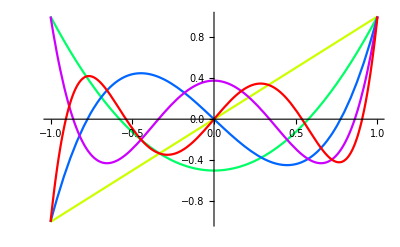

```mathematica
Show[Table[Plot[p[n,x], {x, -1, 1}, PlotStyle->Hue[n/5]], {n,1, 5}]]
```